```mathematica
N@ ((866/397)^3)*93/7;
P1 =10;
P2 = 500;
s1 = 1;(*saturation parameter 397*)
s2 = P2 /P1 *(866/397)^3*93/7*s1; (*saturation parameter 866*)
```

```mathematica
N@ ((866/397)^3)*93/7
```

137.901

```mathematica
s2
```

3019997816400/437995411

```mathematica
H=({{Subscript[Δ, g], Subscript[Ω, 12]/2, 0}, {Subscript[Ω, 12]/2, 0, Subscript[Ω, 23]/2}, {0, Subscript[Ω, 23]/2, Subscript[Δ, r]}});
H1=H/.{Subscript[Ω, 12]->√s1*2π*22*0.93/√2,Subscript[Ω, 23]->0,Subscript[Δ, r]-> 0}
```

{{Δ_g,45.4507,0},{45.4507,0,0},{0,0,0}}

```mathematica
Subscript[C, 1]=√(2π*22*0.93)({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}); (*P-S decay*)
Subscript[C, 2]=√(2π*22*0.07)({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});(*P-D decay*)
Do[Subscript[CC, m]=(Subscript[C, m])†.Subscript[C, m],{m,2}];
```

```mathematica
H1
```

{{Δ_g,45.4507,0},{45.4507,0,0},{0,0,0}}

```mathematica
Evo[δ_,T_]:=Module[{r,H=H1/.{Subscript[Δ, g]->δ}},(*for scaning cooling light*)
r=NDSolveValue[{ ρ'[t]==-ⅈ(H.ρ[t]-ρ[t].H)-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ[t]+ ρ[t].Subscript[CC, m] -2 Subscript[C, m] .ρ[t] .(Subscript[C, m])†),ρ[0]==KroneckerProduct[UnitVector[3,1],UnitVector[3,1]]},ρ, {t,0,T} ];
Re@Diagonal@r[T]
]
```

```mathematica
data=Table[{x,Evo[-20*2π,x]},{x,0,2,0.002}];(*Cooling rate*)
```

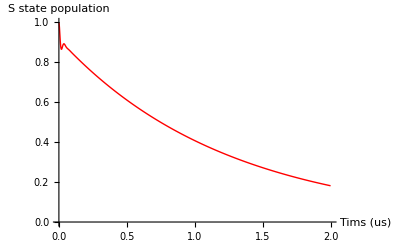

```mathematica
ListLinePlot[{{data⟦All,1⟧,data⟦All,2,1⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"Tims (us)","S state population"}]
```

```mathematica
foo[30]
```

foo[30]

```mathematica
H2
```

{{Δ_g,7.2337,0},{7.2337,0,45.211},{0,45.211,40}}

```mathematica
H2=H/.{Subscript[Δ, r]->40,Subscript[Ω, 12]->√s1*22*0.93/√2,Subscript[Ω, 23]->√s2*22*0.07/√2};
scanblue[δ_]:=Module[{r,H=H2/.{Subscript[Δ, g]->δ},ρ},

ρ=Table[Subscript[r, {i,j}],{i,3},{j,3}];
r=ρ/.NSolve[ {ⅈ(H.ρ-ρ.H)==-1/2∑_(m=1)^2 (Subscript[CC, m]. ρ+ ρ.Subscript[CC, m] -2 Subscript[C, m] .ρ.(Subscript[C, m])†),Total[Diagonal[ρ]]==1},Flatten[ρ]]⟦1⟧;
Re@Diagonal@r
];

scanblue[-10]
```

{0.980439,0.00946392,0.0100967}

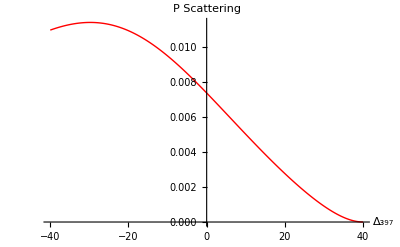

```mathematica
data2=Table[{x,scanblue[x]},{x,-40,40,0.1}];
ListLinePlot[{{data2⟦All,1⟧,data2⟦All,2,2⟧}ᵀ},PlotRange->Full,PlotStyle->Directive[Red,Thick],AxesLabel->{"Δ_397","P Scattering"}]
```

```mathematica
0.07*√(1+(4/0.21)^2)
```

1.33517

```mathematica
(π * 500^2)/0.397
```

1.97833×10^6

```mathematica
1*√(1+(2000/((π * 1^2)/0.397))^2)
```

252.74